```mathematica
Clear[coord,L,nPart,dt,dx,k,s,xPos,u0,myTemp,uTemp,rightT,leftT,lastT,newT,newT];

L:=1                                 (*Length of rod *)
nPart:=10                     (*Number of partitions *)
nTsamples:=100        (*Number of time samples*)
tTime:=10                  (*How much time*)
dt:=tTime/nTsamples       (*Time interval size Δt*)
dx:=L/nPart                         (*Section size Δx*)
k:=1                                          (*k value*)
(*s=k*dt/(dx^2)*)                   (*s constant*)
s=0.50
(*Interesting to note that forcing various *)
(*values on s affects the stability of the solution*)

(*Here I define a function for the initial temperature distribution f0=f(x)*)

(*f0[x_]:=Abs[Sin[6x]]+.2*)

f0[x_]:=Piecewise[{{0,x≥0&&x<0.5L},{(x-0.5L)/L,x≥0.5L&&x<0.75L},{(0.75L-x)/L+0.25,x≥0.75L&&x≤L}}]

(*Here is where I define the initial conditions at t=0*)
(*so u(x,0)=the function f0=f(x) acting on the xpos*)
xPos:=(Range[nPart]-1)*dx

(*This includes the very end of the rod*)
AppendTo[xPos,dx*nPart];

(*the symbol /@ maps the function onto xpos*)
u0:=f0/@xPos

(*Initialize the empty u temperature list, these are*)
(*our sample solution points*)
uTemp:={}

(*At t=1 we have our u0 list of temps*)
uTemp=Append[uTemp,u0];

(*This nested for loop sequence calculates the temps at time*)
(*t by using the difference equation on page 226 of the book*)
(*this is also the same one we derived in class*)

(*The outer loop only starts at t=2 because at t=1 this is t0 with*)
(*initial temp of u0 which we append before the loop*)
For[t=2,t≤nTsamples,t++,

(*Initialize an empty temporary list*)
myTemp:={};

(*This loop is where we go throuh each x and calculate*)
(*u(x,t), where t is from the outer loop*)
For[k=1,k≤nPart+1,k++,     (*Remember we added the end*)
lastT=uTemp[[t-1,k]];          (*so we need to go nPart+1*)

(*if we are at start position x0 or in this case x1*)
If[k==1,rightT=0; 
leftT=uTemp[[t-1,k+1]]];

(*if we reach the end of the rod*)
If[k==nPart+1,leftT=0;rightT=uTemp[[t-1,k-1]]];

(*if we are inside rod*)
If[k>1&&k<nPart+1, 
rightT=uTemp[[t-1,k-1]];
leftT=uTemp[[t-1,k+1]]
];

(*This is the relationship: u[j][m+1]=u[j][m]...from page 226*)
newT=lastT+s*(leftT-2*lastT+rightT);

(*append temperatures to temporary list we started with*)
myTemp=Append[myTemp,newT];
];

(*append the temp list to our uTemp list which we began before*)
(*the outer loop*)
uTemp=Append[uTemp,myTemp];
];
```

0.5

```mathematica
(*Here we define individual frames representing the solution*) (*at different times of t*)

(*Initialize an empty frame list, we will collect the frames*)
frames:={}

(*We need to get the coordinates of the xpos and utemp at*)
(*those xpos at time t here I accidentally used the letter k instead*)
For[k=1, k≤nTsamples,k++,
coord:={};

For[i=1,i≤nPart+1,i++,
coord=Append[coord,{xPos[[i]],uTemp[[k,i]]}];
];

tempframe:=ListLinePlot[coord,PlotRange->{-0.01,0.25}];
frames=Append[frames,tempframe];
];

(*Try manipulating the plot*)
Manipulate[Show[frames[[n]]],{n,1,nTsamples,1}]
```

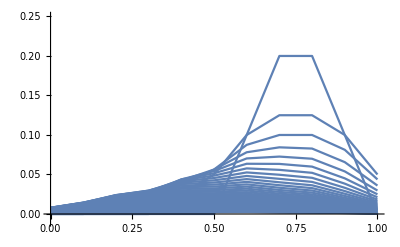

```mathematica
(*Here are the snapshots of the solution*)
myTablePlot=Table[Graphics[frames[[n]]],{n,1,nTsamples,2}];
Show[myTablePlot]
```

```mathematica
(*This will generate a contour and 3d plot overlayed together*)
coord:={};

For[t=1, t≤nTsamples,t++,
For[i=1,i≤nPart+1,i++,
coord=Append[coord,{xPos[[i]],(t-1)*dt,uTemp[[t,i]]}];
];
];

ctPlot=ListContourPlot[coord,ColorFunction->"Rainbow"];
listPlot=ListPlot3D[coord,ColorFunction->"Rainbow",PlotRange-> {-.01,0.25}];

level=-0.01;gr=Graphics3D[{Texture[ctPlot],EdgeForm[],Polygon[{{0,0,level},{L,0,level},{L,tTime,level},{0,tTime,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->{{"Ambient", White}}];

Show[listPlot,gr,PlotRange-> {-.01,0.21},BoxRatios->{1, 1, 1}]
(*Notice that the plot somewhat jagged on some of the contours starting to become unstable! for s = 0.50*)
```

-Graphics3D-